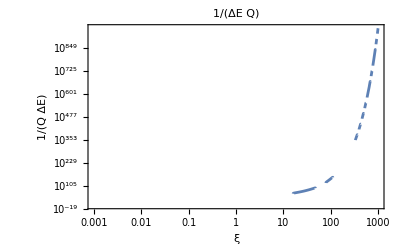

```mathematica
y=(Cos[ξ(d-1)]Sinh[ξ(d+1)]+Cos[ξ(d+1)]Sinh[ξ(1-d)]-Sin[ξ(d-1)]Cosh[ξ(1+d)]+Sin[ξ(1+d)]Cosh[ξ(1-d)]-2ξ(Cos[ξ(d-1)]Cosh[ξ(1+d)]+Cos[ξ(d+1)]Cosh[ξ(1-d)]))/.
{d->1.1};

g=LogLogPlot[y,{ξ,0.001,1000},PlotLabel->Q^-1/ΔE, Frame->True,FrameLabel->{ξ,Q^-1/ΔE}]
```

Set::write: -(3 (-2 ξ (Cos[Times[«2»]] Cosh[Times[«2»]]+Cos[Times[«2»]] Cosh[Times[«2»]])-Cosh[(1+d) ξ] Sin[(-1+d) ξ]+Cosh[(1+Times[«2»]) ξ] Sin[(1+d) ξ]+Cos[(1+d) ξ] Sinh[(1+Times[«2»]) ξ]+Cos[(-1+d) ξ] Sinh[(1+d) ξ]))/(4 ξ^3 (Cos[2 d ξ]+Cosh[2 d ξ]))/.3/4 Abs[(-2 ξ (Times[«2»]+Times[«2»])-Cosh[Times[«2»]] Sin[Times[«2»]]+Cosh[Times[«2»]] Sin[Times[«2»]]-Cos[Times[«2»]] Sinh[Times[«2»]]+Cos[Times[«2»]] Sinh[Times[«2»]])/(ξ^3 (Cos[Times[«2»]]+Cosh[Times[«2»]]))]のタグReplaceAllはProtectedです．

Set::write: Abs[TerminatedEvaluation[RecursionLimit]][n]のタグAbsはProtectedです．

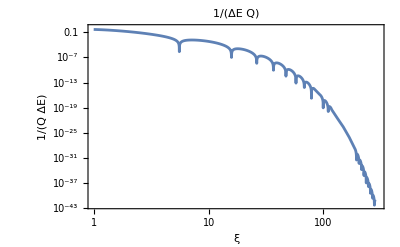

```mathematica
f[n]=3/(4 ξ^3)-1/(Cos[2 d ξ]+Cosh[2 d ξ])(Cos[ξ(d-1)]Sinh[ξ(d+1)]+Cos[ξ(d+1)]Sinh[ξ(1-d)]-Sin[ξ(d-1)]Cosh[ξ(1+d)]+Sin[ξ(1+d)]Cosh[ξ(1-d)]-2ξ(Cos[ξ(d-1)]Cosh[ξ(1+d)]+Cos[ξ(d+1)]Cosh[ξ(1-d)]))/.
QHeatFlow=Abs[f]/.
{d->1.3,ξ->(2n+1)/(2(d-1))π,n->0};
QHeatFlowg=LogLogPlot[QHeatFlow,{ξ,1,300},PlotLabel->Q^-1/ΔE, Frame->True,FrameLabel->{ξ,Q^-1/ΔE}]
```

Q^-1/ΔEの分子の微分

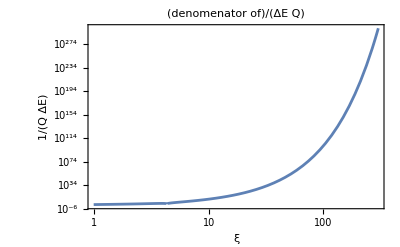

```mathematica
fnd=-2d(-1)^n Sinh[ξ(d+1)]-2d Sin[ξ(d+1)]Sinh[ξ(1-d)]+2ξ((d-1)(-1)^n Cosh[ξ(1+d)]+(d+1)Sin[ξ(1-d)]Cosh[ξ(1-d)]-(1-d)Cos[ξ(1+d)]Sinh[ξ(1-d)])/.
{d->1.3,n->0};
fndg=LogLogPlot[Abs[fnd],{ξ,1,300},PlotLabel->denomenator of Q^-1/ΔE, Frame->True,FrameLabel->{ξ,Q^-1/ΔE}]
```

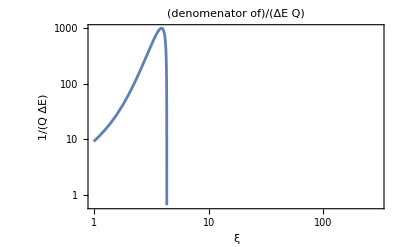

```mathematica
fnd=-2d(-1)^n Sinh[ξ(d+1)]-2d Sin[ξ(d+1)]Sinh[ξ(1-d)]+2ξ((d-1)(-1)^n Cosh[ξ(1+d)]+(d+1)Sin[ξ(1-d)]Cosh[ξ(1-d)]-(1-d)Cos[ξ(1+d)]Sinh[ξ(1-d)])/.
{d->1.3,n->1};
fndg=LogLogPlot[fnd,{ξ,1,300},PlotLabel->denomenator of Q^-1/ΔE, Frame->True,FrameLabel->{ξ,Q^-1/ΔE}]
```

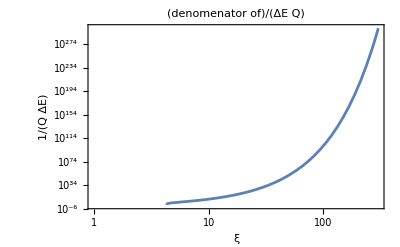

```mathematica
fnd=-2d(-1)^n Sinh[ξ(d+1)]-2d Sin[ξ(d+1)]Sinh[ξ(1-d)]+2ξ((d-1)(-1)^n Cosh[ξ(1+d)]+(d+1)Sin[ξ(1-d)]Cosh[ξ(1-d)]-(1-d)Cos[ξ(1+d)]Sinh[ξ(1-d)])/.
{d->1.3,n->2};
fndg=LogLogPlot[fnd,{ξ,1,300},PlotLabel->denomenator of Q^-1/ΔE, Frame->True,FrameLabel->{ξ,Q^-1/ΔE}]
```

```mathematica
fnd=-2d(-1)^n Sinh[ξ(d+1)]-2d Sin[ξ(d+1)]Sinh[ξ(1-d)]+2ξ((d-1)(-1)^n Cosh[ξ(1+d)]+(d+1)Sin[ξ(1-d)]Cosh[ξ(1-d)]-(1-d)Cos[ξ(1+d)]Sinh[ξ(1-d)])/.
{d->1.3,n->3};
fndg=LogLogPlot[fnd,{ξ,1,300},PlotLabel->denomenator of Q^-1/ΔE, Frame->True,FrameLabel->{ξ,Q^-1/ΔE}]
```

-Graphics-